```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f,m,r,w,v,sc,g]
```

```mathematica
(*m003(-4,1)*)
p[z_]=z^5-z^3-z^2+z+1
```

1+z-z^2-z^3+z^5

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[x],x]]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{-1,-1,1,1,0}}

```mathematica
N[Eigenvalues[m]]
```

{1.04575+0.405588 ⅈ,1.04575-0.405588 ⅈ,-0.699311+0.811268 ⅈ,-0.699311-0.811268 ⅈ,-0.692872}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,5}]
```

{-0.699311-0.811268 ⅈ,-0.699311+0.811268 ⅈ,-0.692872,1.04575-0.405588 ⅈ,1.04575+0.405588 ⅈ}

```mathematica
Abs[%]
```

{1.07107,1.07107,0.692872,1.12165,1.12165}

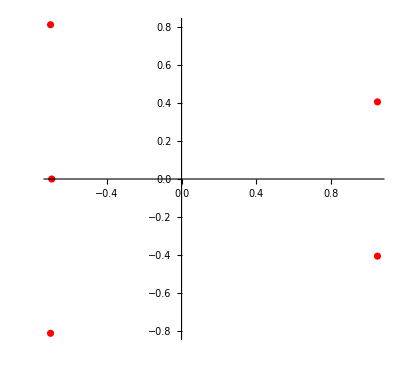

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-0.699311,-0.811268},{-0.699311,0.811268}},{{-0.699311,-0.811268},{-0.692872,0}},{{-0.699311,-0.811268},{-0.699311,0.811268}},{{-0.699311,0.811268},{-0.692872,0}},{{-0.699311,0.811268},{1.04575,-0.405588}},{{-0.692872,0},{1.04575,-0.405588}}}

```mathematica
Table[Eigenvalues[w[[i]]]//Chop,{i,6}]
```

{{1.12265,-1.01069},{-1.17692,0.477607},{1.12265,-1.01069},{-0.349656+0.663209 ⅈ,-0.349656-0.663209 ⅈ},{-1.48516,0.380262},{-0.692872,-0.405588}}

```mathematica
(* Projecting the  3rd Minimal Pisot Polynomial onto a qz^(2*n) Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^6*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^8*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^14*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^16*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
```

```mathematica
g=JuliaSetPlot[f[z,3],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

```mathematica
Export["Julia_5root_m003neg4_1_z10_Herman_rings_Hue_scale2.jpg",g]
```

Julia_5root_m003neg4_1_z10_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```